```mathematica
wd=NotebookDirectory[];
appPath="+mem="<>wd<>"dhrystone.bin";
```

```mathematica
LibraryUnload[libhello]
```

```mathematica
<<"/Users/ckorikov/_syntacore/projects/wolfram_russianhack18_scr1/cpp_bridge/math.m"
```

```mathematica
pclist = Table[nextpc[],10000];
```

```mathematica
g=BlockMap[#[[1]]->#[[2]]&,pclist,2,1];
```

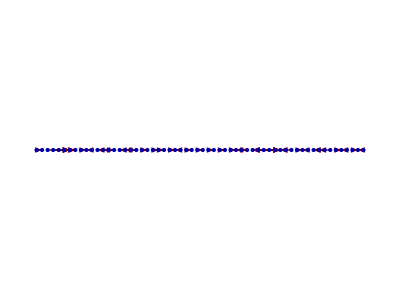

```mathematica
GraphPlot[Select[g,(#[[2]]-#[[1]])>100&],DirectedEdges-> True,Method->"LinearEmbedding"]
```

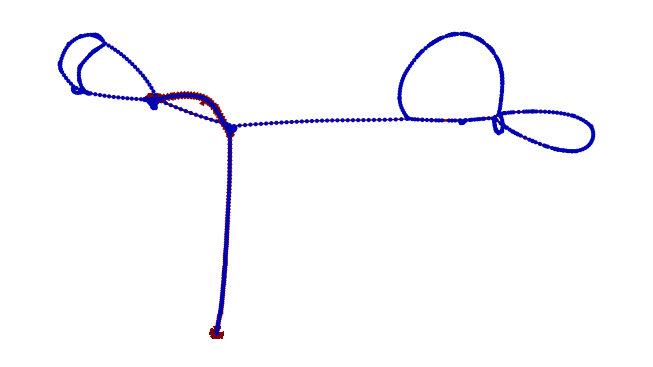

```mathematica
GraphPlot[g[[2000;;9000]],DirectedEdges-> True]
```

```mathematica
Dataset[Table[{i,BaseForm[getregister[i],16],BaseForm[getregister[i],2]},{i,1,31}]]
```

Dataset[<>]

```mathematica
reset["+mem=/Users/ckorikov/_syntacore/projects/wolfram_russianhack18_scr1/cpp_bridge/dhrystone.bin"];
```

```mathematica
regs=Table[{i,getregister[i]},{i,1,31}];
```

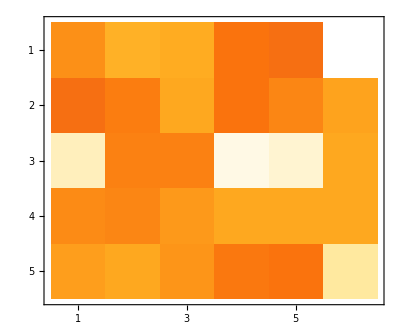

```mathematica
MatrixPlot[BlockMap[#&,Map[#[[2]]&,regs],6],ColorFunction->"SunsetColors"]
```

```mathematica
Table[nextpc[],10000];
```

```mathematica
ListAnimate[Table[nextpc[];MatrixPlot[BlockMap[#&,Map[#[[2]]&,Table[{i,getregister[i]},{i,1,31}]],6],ColorFunction->"SunsetColors"],
1000
]]
```

```mathematica
reglist[]
```

{0,2768,65344,13600,0,-1,1498564676,-1,3,12288,0,67,11648,1230132307,66,66,1380982853,1313821779,12288,500,67,9996,12288,12288,12288,11636,12288,9964,2,0,1095911247}

```mathematica
branchstate[]
```

{512,0,0,0,0}

```mathematica
branchstatelist=Table[nextpc[];branchstate[],20000];
```

```mathematica
Export["branchstatelist.xml",branchstatelist]
```

branchstatelist.xml

```mathematica
readmem[512,100]
```

{151,49,0,0,147,129,1,50,151,53,0,0,147,133,133,179,23,86,0,0,19,6,6,59,33,160,35,160,5,0,145,5,227,157,197,254,23,1,1,0,19,1,193,221,183,2,73,0,5,67,35,160,98,0,183,2,73,0,147,130,66,0,19,3,48,6,35,160,98,0,183,2,73,0,147,130,2,1,125,83,35,160,98,0,35,162,98,0,1,69,129,69,239,0,192,98,111,16,16,50}

```mathematica
While[!isFinished[],
Print[nextpc[]]
]
```

```mathematica
branchstatelist
```

{{516,0,0,0,12800},{520,0,0,0,1316},{524,0,0,0,12808},{528,0,0,0,-700},{532,0,0,0,21008},{536,0,0,0,1476},{544,1,0,0,544},{538,0,1,0,538},{542,0,0,0,11584},{544,0,0,0,546},{538,0,1,0,538},{542,0,0,0,11588},19976,{2878,0,0,0,2},{2880,0,0,0,2878},{2884,0,0,1,2894},{2888,0,0,0,11616},{2892,0,0,0,2896},{2894,0,0,0,2892},{2898,0,0,0,11628},{2900,0,0,0,2898},{2904,0,0,0,11628},{2604,0,1,0,2604},{2608,0,0,0,2668},{2612,0,0,0,11608}}
 |  |  |  |

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544

538

542

544